```mathematica
joueur1Img = -Graphics-;
joueur2Img = -Graphics-;
invalidCellImg = -Graphics-;
WinImg= -Graphics-
```

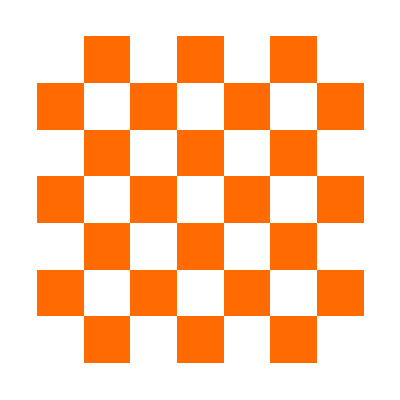

Set::partd: Part specification GridGraphics⟦1⟧ is longer than depth of object.

```mathematica
GridGraphics= cb[n_Integer/;n>0]:=MatrixPlot[SparseArray[{i_,j_}:>Mod[i+j,2],{n,n}],Frame->None]

cb[7]
```

```mathematica
(*Define the two lists of lists*)list1=Table[RandomInteger[100,{5}],{4}];
list2=Table[RandomChoice[{1,Null},{5}],{4}];

(*Create the third list of lists based on the criteria*)
list3=MapThread[MapThread[If[#2===1,#1,Null]&,{#1,#2}]&,{list1,list2}];

(*Display the lists*)
list1
list2
list3
```

{{87,89,62,89,35},{83,96,85,24,57},{6,7,57,74,66},{36,51,88,71,98}}

{{1,Null,Null,Null,Null},{1,1,1,Null,1},{1,1,1,1,1},{Null,1,1,1,1}}

{{87,Null,Null,Null,Null},{83,96,85,Null,57},{6,7,57,74,66},{Null,51,88,71,98}}

```mathematica
MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{list1,list2}]
```

{{10,Null,30,Null},{11,Null,31,Null}}

```mathematica
Isola[] := DynamicModule[
{
infinity = 1000,
displayGrid, graphDestroyGrid, displayMatrix, gridX = 5, gridY = 5, cellSize = 73,destroyMatrix,distanceMatrixRed, distanceMatrixBlue,
moveMatrixRed,moveMatrixBlue, simplerMatrix,displayRedGrid, displayBlueGrid,graphBlueGrid, graphRedGrid,
updateDistances,
terrainMatrix = 0,floor,
terrainGrid,
gridRules = AssociationThread[{-1, 0, 1, 2, 3}, {"floor1", "void", "floor2", "player1", "player2"}],
playingTurnRules = AssociationThread[{0, 1}, {"blue", "red"}],
playingActionRules = AssociationThread[{0, 1}, {"move", "destroy"}],
getTerrain,
centerX, centerY,
whoIsPlaying = 0, currentAction = 0,
changeTurn, changeAction,
position,
init,
updateMatrix,
graybtn, redbtn, bluebtn,
allBlueMatrix, allRedMatrix, allBlackMatrix,preMoveMatrixRed,preMoveMatrixBlue,
moveRed, moveBlue, destroyTile
},
(*variables*)
changeTurn := (whoIsPlaying == Mod[whoIsPlaying + 1, 2]);
centerX = Ceiling@(gridX/2);
centerY = Ceiling@(gridY/2);
position = {{centerX, 1}, {centerX, gridY}};
(*functions*)
init := (
floor = Table[Table[Mod[i+j, 2], {i,gridX}], {j, gridY}]/.{0-> -1};
terrainMatrix = Table[Table[Mod[i+j, 2], {i,gridX}], {j, gridY}]/.{0-> -1};
terrainMatrix[[position[[1]][[1]],position[[1]][[2]]]] = 2;
terrainMatrix[[position[[2]][[1]],position[[2]][[2]]]] = 3;
allBlueMatrix = Table[Table[bluebtn[j,i], {i, gridY}],{j, gridX}];
allRedMatrix = Table[Table[redbtn[j,i], {i, gridY}],{j, gridX}];
allBlackMatrix = Table[Table[graybtn[j,i], {i, gridY}],{j, gridX}];
);

updateMatrix[]:=(
terrainMatrix = floor;
terrainMatrix[[position[[1]][[1]],position[[1]][[2]]]] = 2;
terrainMatrix[[position[[2]][[1]],position[[2]][[2]]]] = 3;
updateDistances[];
Print["update"]
);
(**)
(**)
graybtn[] := Button[Graphics[{Darker[Gray, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
bluebtn[] := Button[Graphics[{Darker[Blue, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
redbtn[] := Button[Graphics[{Darker[Red, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], Print["click"], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
graybtn[x_, y_] := Button[Graphics[{Darker[Gray, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], destroyTile[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
bluebtn[x_, y_] := Button[Graphics[{Darker[Blue, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], moveBlue[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
redbtn[x_,y_] := Button[Graphics[{Darker[Red, 0.5], Circle[{0, 0}, 15], Opacity[0.4], Disk[{0, 0}, 15]}], moveRed[x, y], Method->"Queued", ImageSize -> {10, 10}, Appearance->"Frameless"];
(**)
moveRed[x_, y_] := (
Print["red"];
position[[2]] = {x, y};
updateMatrix[];
);
moveBlue[x_, y_] := (
position[[1]] = {x, y};
updateMatrix[];
Print[terrainMatrix];
);
destroyTile[x_, y_] := (
Print["destroy"];
floor[[x, y]]=0;
updateMatrix[];
);
(**)
(**)
(*--------------------------MATRICES----------------------------------------------------*)
simplerMatrix :=terrainMatrix/.{-1|1 -> 0, 0|2|3 -> infinity};
terrainGrid := terrainMatrix /.{-1 -> Lighter[Yellow, 0.5],0->Black,1->Lighter[Orange, 0.5],2->Null,3->Null};
destroyMatrix := terrainMatrix/.{-1|1 -> graybtn[], 0|2|3 -> Null};
preMoveMatrixRed := distanceMatrixRed/.{1-> redbtn[], x_/;x>1 -> Null};
moveMatrixRed := MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allRedMatrix,preMoveMatrixRed}];
preMoveMatrixBlue := distanceMatrixBlue/.{1-> bluebtn[],x_/;x>1 -> Null};
moveMatrixBlue := MapThread[MapThread[If[#2===Null,Null,#1]&,{#1,#2}]&,{allBlueMatrix, preMoveMatrixBlue}];
updateDistances := (
distanceMatrixRed:= simplerMatrix;
distanceMatrixRed = Table[Table[distanceMatrixRed[[j,i]]+Max[Abs[position[[2, 1]] - j],Abs[position[[2, 2]] - i]], {i, gridY}],{j, gridX}];

distanceMatrixBlue:= simplerMatrix;
distanceMatrixBlue = Table[Table[distanceMatrixBlue[[j,i]]+Max[Abs[position[[1, 1]] - j],Abs[position[[1, 2]] - i]], {i, gridY}],{j, gridX}];
);
(*<<<--------------------------<<<*)

displayGrid[] := Grid[terrainGrid, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
displayBlueGrid[] := Grid[distanceMatrixBlue, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
displayRedGrid[] := Grid[distanceMatrixRed, Frame->None,  Alignment->{Center, Center}, ItemSize->{5, 5}];
graphDestroyGrid[] := GraphicsGrid[destroyMatrix, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
graphRedGrid[] := GraphicsGrid[moveMatrixRed, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
graphBlueGrid[] := GraphicsGrid[moveMatrixBlue, 
Frame->None,  Alignment->{Center, Center}, 
ItemAspectRatio->1 (*ImageSize-> {gridX*cellSize, gridY * cellSize}*)
];
displayMatrix[] := MatrixPlot[terrainMatrix, Frame->None, ColorRules->{-1 -> Lighter[Yellow, 0.5],0->Black,1->Lighter[Orange, 0.5],2->Blue,3->Red}, Background->LightBlue];

(*position[[1, 1]] = 2;
position[[2, 1]] = 4;
position[[2, 2]] = 3;
floor[[3, 3]] = 0;
floor[[3, 2]] = 0;
*)
updateMatrix[];

Dynamic@Overlay[{displayMatrix[], graphBlueGrid[]}, None, 2]
];
```